```mathematica
h=Flatten[Table[x^n  ,{n,0,3}]];
```

```mathematica
M=Flatten[Table[{a},{a,0,1}],1];M//MatrixForm
```

(0
1)

```mathematica
A[i_]:=D[#,{x,M[[i]]}]&
```

```mathematica
Collect[{s1,s2,s3,s4}.P[breite].Co.h/.x->y/breite,{s1,s2,s3,s4}]/.y->x
```

{s1,s2,s3,s4}.P[breite].Co.{1,x/breite,x^2/breite^2,x^3/breite^3}

```mathematica
CForm[%]
```

Dot(List(s1,s2,s3,s4),P(breite),Co,List(1,x/breite,Power(x,2)/Power(breite,2),Power(x,3)/Power(breite,3)))

```mathematica
Co=Inverse[Transpose[Flatten[Table[A[j][h]/.x->M[[i]],{j,2},{i,2}],1]]]
```

{{1,0,-3,2},{0,0,3,-2},{0,1,-2,1},{0,0,-1,1}}

```mathematica
P[m_ ]:=DiagonalMatrix [  {1,1,m,m}];
```

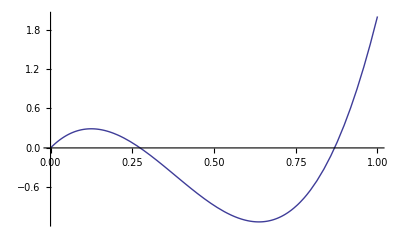

```mathematica
s={0,2,5,20};Plot[s.Co.h,{x,0,1}]
```

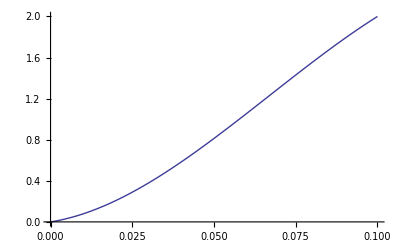

```mathematica
s={0,2,5,20};b=0.1;
Plot[{s.P[b].Co.h/.x->y/b},{y,0,b}]
```

```mathematica
A=20;nx=20;ny=20;of=0.0001;M2=Flatten[Table[Join[{x/nx+of,y/ny+of},Table[ND[f2[#1,#2,0.999,A]&,i,x/nx+of,y/ny+of],{i,4}]],{x,nx},{y,ny}]//N,1];
```

```mathematica
ListPointPlot3D[Transpose[Transpose[M2 ][[1;;3]]]]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[Transpose[M2 ][[1;;3]]]]
```

-Graphics3D-

```mathematica
Plot3D[f2[x,y,0.999,A],{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
nD[f_,x_]:=(f[x+of]-f[x-of])/2/dof;
```

```mathematica
dof=0.000001;ND[f_,i_,x_,y_]:=Switch[i,1,f[x,y],2,nD[f[#,y]&,x],3,nD[f[x,#]&,y],4,-(-f[x-dof,y-dof]+f[x-dof,y+dof]+f[x+dof,y-dof]-f[x+of,y+dof])/(4dof^2)];
```

```mathematica
ND
```

```mathematica
ND[f2[#,.9999,0.999,A]&,0.2]
```

1.13539×10^-10

```mathematica
ND[f2[#1,#2,0.999,A]&,2,1,yy]
```

nD[(f2[#1,#2,0.999,A]&)[#1,0.7]&,1]

```mathematica
f2[x_,y_,a_,b_]:=Sin[x]Cos[y]
```

```mathematica
D[D[f2[X,Y,0.999,A],X],Y]/.Y->y/.X->x
```

-Cos[x] Sin[y]

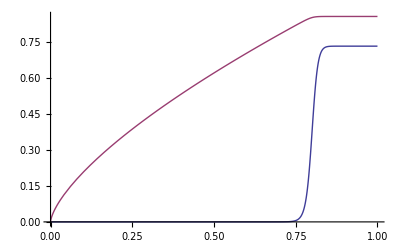

```mathematica
yy=0.8;Plot[{ND[f2[#1,#2,0.999,A]&,3,x,yy],f2[x,yy,0.999,A]},{x,0,1}]
```

```mathematica
f2[x,yy,0.99,A],x]/.x->xx
```

FindRoot::nlnum: The function value {-0.99 + 2.71828^(« 23 » + « 1 »)^1/20 - 1.\ « 1 »^« 1 »\ (« 1 »)^39 « 1 » « 2 »\ (19.  + (« 1 »)^1/20)/19.  + (1.11033×10^-9 + « 1 »)^1/20} is not a list of numbers with dimensions {1} at {z} = {1.×10^-13}.

ND[-0.99,0.1]

```mathematica
f2[x,y,z,a]
```

FindRoot::nlnum: The function value {-1.×10^-13 + 2.71828^(« 1 » + « 1 »)^1/a - 1.\ « 1 »^« 1 »\ (« 1 »)\ (« 1 »/« 1 »)^2.  - « 3 »/a/-1. + a + (Power[« 2 »] + Power[« 2 »])^1/a} is not a list of numbers with dimensions {1} at {z} = {1.×10^-13}.

-z